# 1D linear stability analysis (LSA) robustness sweep for the switch model

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm

```mathematica
params={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3*4,
kdD->0.0015*4,
kdEr->1.5*4,
kdEl->10^-5*4,
kde->1,
λ->5,
μ->20
};
```

## Setup

Setup the reaction terms for the 1+1D switch model

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

### Phase diagram sweep

Sweep the total average concentrations rhoD and rhoE

```mathematica
ClearAll@instabSweep;
Options[instabSweep]=Options[testInstab];
instabSweep[params_,variedParams_,opts:OptionsPattern[]]:=Block[{
parameterNames=ToString[#[[1]]]&/@variedParams,variedParamComs=Flatten[Outer[List,Sequence@@(variedParams[[All,2]])],Length[variedParams]-1],
densities
},
densities=Reap[Do[Block[{
ps=Join[Thread[variedParams[[All,1]]->vps],DeleteCases[params,Alternatives[Sequence@@((#[[1]]->_)&/@variedParams)]]],
instab
},
instab=testInstab[ps];

If[instab[[1]]>1,
Sow@{vps,instab[[1]],instab[[2]],instab[[-1]]};,
Sow@{vps,instab[[1]]};
]

],{vps,variedParamComs}];
][[-1]];
densities[[1]]
];
```

## LSA

Calculate the LSA phase diagrams for several combinations of kdEr and kdEl

```mathematica
instabList=ParallelTable[
Print["parameters: ",ks];
{
ks,
instabSweep[Join[{kdEr->ks[[1]],kdEl->(ks[[2]])},DeleteCases[params,(kdEr->_)|(kdEl->_)]],
{
{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}
}
]
},{ks,Flatten[Outer[List,10^Range[-2,1,1]*4,10^Range[-5,-1,1]*4],1]},"Method"->"FinestGrained"];
```

parameters: {1/25,1/25000}

parameters: {1/25,1/2500}

parameters: {1/25,1/250}

parameters: {1/25,1/25}

parameters: {1/25,2/5}

parameters: {2/5,1/25000}

parameters: {2/5,1/2500}

parameters: {2/5,1/250}

parameters: {2/5,1/25}

parameters: {2/5,2/5}

parameters: {4,1/25000}

parameters: {4,1/2500}

parameters: {4,1/250}

parameters: {4,1/25}

parameters: {4,2/5}

parameters: {40,1/25000}

parameters: {40,1/2500}

parameters: {40,1/250}

parameters: {40,1/25}

parameters: {40,2/5}

## Analysis

## Instability region (rates labeled as the 2+3D rates)

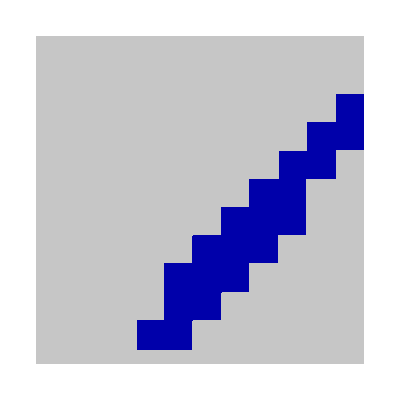
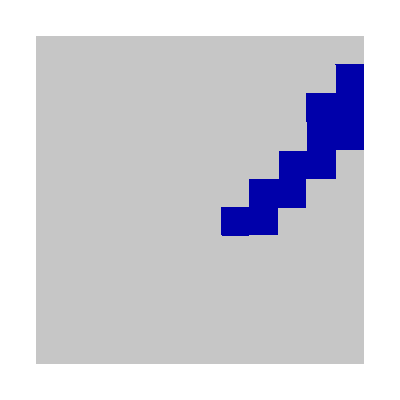
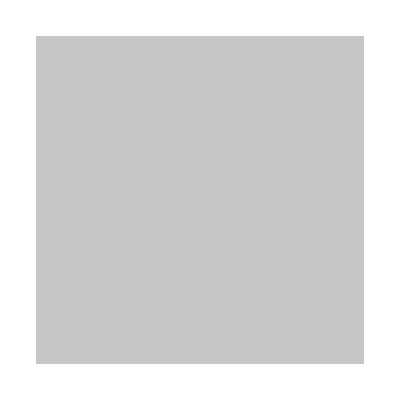
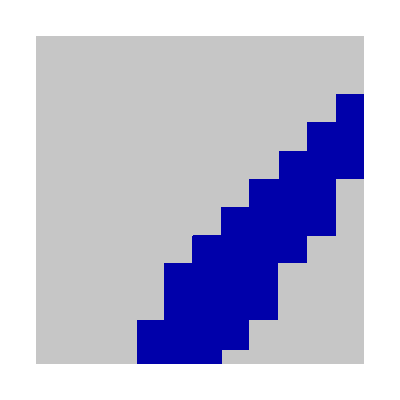
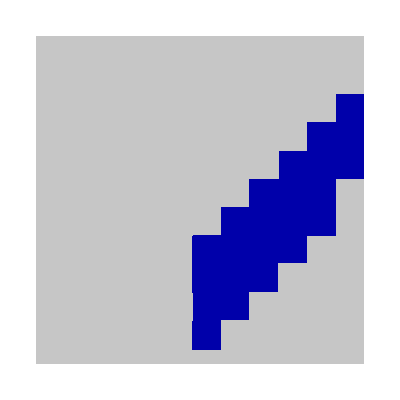
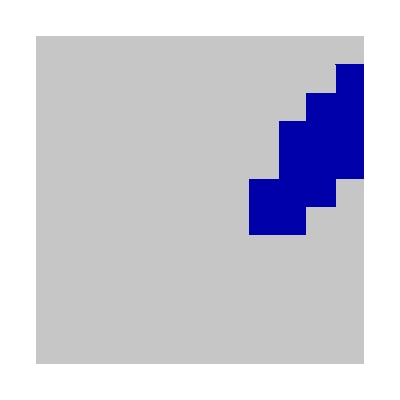
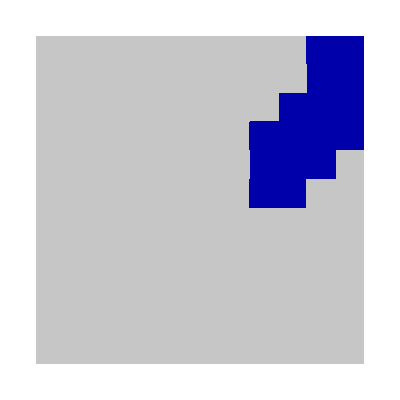
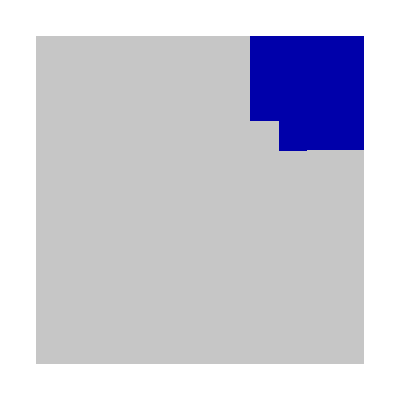
| kdEl = 1/10 | kdEl = 1/100 | kdEl = 1/1000 | kdEl = 1/10000 | kdEl = 1/100000
kdEr = 1/100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kdEr = 1/10 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kdEr = 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kdEr = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["kdEr = "<>ToString[#,TraditionalForm],Black]&/@(10^Range[-2,1,1])]},Transpose@
Join[
{Style["kdEl = "<>ToString[#,TraditionalForm],Black]&/@(Reverse[10^Range[-5,-1,1]])},

(Function[data,
ListDensityPlot[Join[
{Log10[4#[[1,1]]],Log10[4#[[1,2]]],If[#[[2]]==0,0,If[#[[2]]==-1,-1,1]]}&/@data[[2]]
],
InterpolationOrder->0,
ColorFunction->(If[#==-1,White,If[#==0,Lighter@Lighter@Gray,Darker@Blue]]&),
ColorFunctionScaling->False,
PlotRange->{{2,4.3},{2,4.3},All},
FrameTicks->None,
Frame->None]
]/@Reverse[#]&)/@(Partition[instabList,Length[10^Range[-5,-1,1]]])
]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"LSA-robustnessSweep.pdf",
Grid[
Transpose@Join[{Join[{Null},Style["kdEr = "<>ToString[#,TraditionalForm],Black]&/@(10^Range[-2,1,1])]},Transpose@
Join[
{Style["kdEl = "<>ToString[#,TraditionalForm],Black]&/@(Reverse[10^Range[-5,-1,1]])},

(Function[data,
ListDensityPlot[Join[
{Log10[4#[[1,1]]],Log10[4#[[1,2]]],If[#[[2]]==0,0,If[#[[2]]==-1,-1,1]]}&/@data[[2]]
],
InterpolationOrder->0,
ColorFunction->(If[#==-1,White,If[#==0,Lighter@Lighter@Gray,Darker@Blue]]&),
ColorFunctionScaling->False,
PlotRange->{{2,4.3},{2,4.3},All},
FrameTicks->None,
Frame->None]
]/@Reverse[#]&)/@(Partition[instabList,Length[10^Range[-5,-1,1]]])
]
]
]
]
```